```mathematica
(*d,d,u,u ̄,s,s ̄,c,c ̄,b,b,I,J,P*)
```

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cmishra/Projects/BaryonsFromMesons/GPML/FinalResultsGP

```mathematica
(*general*)
MeanStdExpScale[μ_,σ_]:=Return[{Exp[μ+σ^2/2],Exp[2μ+σ^2](Exp[σ^2]-1)}]
BoundsExpScale[μ_,σ_]:=Return[{Exp[μ+σ^2/2],(Exp[2μ+σ^2](Exp[σ^2]-1))^(1/2)(*Exp[μ]-Exp[μ-σ],Exp[μ+σ]-Exp[μ]*)}]
ExpMean[μ_,σ_]:=Exp[μ+σ^2/2];
ExpMeans[μs_,σs_]:=Table[Exp[μs[[i]]+σs[[i]]^2/2],{i,Length[μs]}];
TR[a_,b_]:=Thread[Rule[a,b]];
DD:=DeleteDuplicates;
NN[x_]:=N[x,20];

MeanErrors[preds_,true_]:=Module[{X},
(* returns mean absolute error and standard deviation of absolute error *)
X=Abs[(preds-true)/true];
Return[{Mean[X],StandardDeviation[X]}]];

TakeMean[x_]:=If[Length[x]>0,Return[x[[1]]],Return[x]](* for numbers of the form Around *)

MM[l_List]:=Module[{p,r,pr},If[MatrixQ[l],Return[l//MatrixForm],p=Position[l,_?MatrixQ,Infinity];
r=Map[MatrixForm,Cases[l,_?MatrixQ,Infinity]];
pr=Table[p[[i]]->r[[i]],{i,1,Length[p]}];
ReplacePart[l,pr]]];

(*ErrorsNat[v1_,v2_]:=Total[100*(Abs[Exp[v1]-Exp[v2]]/Exp[v1])]/Length[v1];*)
ErrorsNatStd[trues_,μs_,σs_]:=Total[100*(Abs[Exp[trues]-ExpMeans[μs,σs]]/Exp[trues])]/Length[trues];

ListAllErrors[Mtrue_,Btrue_,Etrue_,Mmean_,Bmean_,Emean_,Mstd_,Bstd_,Estd_,QmodelM_,QmodelB_,QmodelE_]:=Module[{MesonicErrors,(*MesonicErrorsP,*)BaryonicErrors,(*BaryonicErrorsP,*)ExoticErrors(*,ExoticErrorsP*)},
MesonicErrors={ErrorsNatStd[Mtrue,QmodelM[[;;,2]],Table[0,{Length[Mtrue]}](*QModel std dev =0 *)],ErrorsNatStd[Mtrue,Mmean,Mstd]};
BaryonicErrors={ErrorsNatStd[Btrue,QmodelB[[;;,2]],Table[0,{Length[Btrue]}]],ErrorsNatStd[Btrue,Bmean,Bstd]};
ExoticErrors={ErrorsNatStd[Etrue,QmodelE[[;;,2]],Table[0,{Length[Etrue]}]],ErrorsNatStd[Etrue,Emean,Estd]};

(*MesonicErrorsP={ErrorsNat[MtrueP,QmodelMP[[;;,2]]],ErrorsNat[MtrueP,MpredsP]};
BaryonicErrorsP={ErrorsNat[BtrueP,QmodelBP[[;;,2]]],ErrorsNat[BtrueP,BpredsP]};
ExoticErrorsP={ErrorsNat[EtrueP,QmodelEP[[;;,2]]],ErrorsNat[EtrueP,EpredsP]};*)

Print["Errors on Full Dataset"];
Print["Mesonic Errors:      Quark Model, GP Model : ",MesonicErrors];
Print["Baryonic Errors:     Quark Model, GP Model : ",BaryonicErrors];
Print["Exotic State Errors: Quark Model, GP Model : ",ExoticErrors];

(*Print["Errors on Partial Dataset"];
Print["Mesonic Errors:      Quark Model, GP Model : ",Chop[MesonicErrorsP,10^-7]];
Print["Baryonic Errors:     Quark Model, GP Model : ",BaryonicErrorsP];
Print["Exotic State Errors: Quark Model, GP Model : ",ExoticErrorsP];*)
];

funcPlot[data_,PR_]:=Show[
col=Red;
col1=RGBColor[0.368417,0.506779,0.709798];
ListPlot[data,IntervalMarkers->"Fences",
(*AxesLabel->{"Log Measured masses (MeV) ", "Log Predicted masses (MeV)"},*)PlotRange->PR,PlotStyle->{Directive[PointSize[Medium],col1]},PlotRangeClipping->False,(*PlotLegends->Placed[legends={"GP predictions","Quark Model Predictions"},Right],*)ImageSize->Large],
a=PR[[2,1]];b=PR[[1,2]];

Plot[Log[10/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}],
Plot[x,{x,a,b},PlotRange->PR,PlotStyle->{Black,Dashed}],
Plot[Log[8/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}]];

funcPlotNoLines[data_,PR_]:=Show[
col1=RGBColor[0.368417,0.506779,0.709798];
a=PR[[2,1]];b=PR[[1,2]];
ListPlot[data,IntervalMarkers->"Fences",
(*AxesLabel->{"Log Measured masses (MeV) ", "Log Predicted masses (MeV)"},*)PlotRange->{a,b},PlotStyle->{Directive[PointSize[Medium],col1]},PlotRangeClipping->False,(*PlotLegends->Placed[legends={"GP predictions","Quark Model Predictions"},Right],*)ImageSize->Large],

(*Plot[Log[10/9]+x,{x,a,b},PlotRange->{{a,b},{a,b}},PlotStyle->{Gray,Dashed}],*)
Plot[x,{x,a,b},PlotRange->PR,PlotStyle->{Black,Dashed}]
(*,Plot[Log[8/9]+x,{x,a,b},PlotRange->{{a,b},{a,b}},PlotStyle->{Gray,Dashed}]*)];


funcPlotQM[data1_,data2_,PR_]:=Show[
col=Red;
col1=RGBColor[0.368417,0.506779,0.709798];
a=PR[[2,1]];b=PR[[1,2]];
ListPlot[{data1,data2},IntervalMarkers->"Fences",PlotRange->PR,PlotStyle->{{Directive[PointSize[Medium],col1]},{Directive[PointSize[Medium],Green],Dashed}},PlotRangeClipping->False,(*PlotLegends->Placed[legends={"GP predictions","Quark Model Predictions"},Right],*)ImageSize->Large,Frame->True,FrameLabel->{"Measured mass (MeV, Log Scale) ", "Predicted mass (MeV, Log Scale)"}],
col=Red;

Plot[Log[10/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}],
Plot[x,{x,a,b},PlotRange->PR,PlotStyle->{Black,Dashed}],
Plot[Log[8/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}]];

funcPlotQMNoLines[data1_,data2_,PR_]:=Show[
col1=RGBColor[0.368417,0.506779,0.709798];
a=PR[[2,1]];b=PR[[1,2]];
ListPlot[{data1,data2},IntervalMarkers->"Fences",
(*AxesLabel->{"Log Measured masses (MeV) ", "Log Predicted masses (MeV)"},*)PlotRange->PR,PlotStyle->{{Directive[PointSize[Medium],col1]},{Directive[PointSize[Medium],Orange],Dashed}},PlotRangeClipping->False,(*PlotLegends->Placed[legends={"GP predictions","Quark Model Predictions"},Right],*)ImageSize->Large],

(*Plot[Log[10/9]+x,{x,a,b},PlotRange->{{a,b},{a,b}},PlotStyle->{Gray,Dashed}],*)
Plot[x,{x,a,b},PlotRange->PR,PlotStyle->{Black,Dashed}]
(*,Plot[Log[8/9]+x,{x,a,b},PlotRange->{{a,b},{a,b}},PlotStyle->{Gray,Dashed}]*)];
```

```mathematica
(*#################### NN data ########################### *)
MesonicData100={{4.938570638077743,6.540.23},{4.938570638077743,6.530.23},{4.905104393553379,6.530.23},{6.306023430417303,6.910.09},{6.214608098422191,6.900.10},{6.653198456962184,7.210.05},{6.653198456962184,7.210.05},{6.653198456962184,7.190.06},{6.662685597334232,7.120.07},{6.864618106504443,7.070.05},{6.887552571664617,6.9100.030},{6.927029335236704,7.190.06},{7.064759027791802,7.1660.033},{7.1143628616562475,7.2300.024},{7.1143628616562475,7.2060.028},{7.1143628616562475,7.1980.031},{7.114769448366463,7.2300.024},{7.114769448366463,7.2060.028},{7.114769448366463,7.1980.031},{7.1510935375818665,7.540.04},{7.156098631318089,7.1660.033},{7.165493475060845,6.910.09},{7.170119543449628,6.530.23},{7.170119543449628,6.540.23},{7.170119543449628,6.530.23},{7.184098306763924,7.3220.028},{7.184098306763924,7.3370.032},{7.184098306763924,7.3450.031},{7.222566018822171,6.900.10},{7.21081845347222,7.190.06},{7.21081845347222,7.210.05},{7.21081845347222,7.210.05},{7.250493557181996,6.910.09},{7.255591274253665,7.2610.011},{7.262838957529376,7.2610.011},{7.258412150595307,7.120.07},{7.295735072749282,7.2300.024},{7.289610521451167,7.210.05},{7.289610521451167,7.210.05},{7.297091005160418,7.070.05},{7.315883504509785,6.900.10},{7.329749689041512,7.3200.024},{7.415776975415394,7.190.06},{7.415776975415394,7.210.05},{7.415776975415394,7.210.05},{7.411556287811163,7.2300.024},{7.411556287811163,7.2060.028},{7.411556287811163,7.1980.031},{7.388327859577107,7.3490.035},{7.4205789054108005,7.120.07},{7.418780882750794,7.4350.027},{7.420938122321806,7.4670.025},{7.420938122321806,7.4780.030},{7.420938122321806,7.4820.029},{7.426549072397305,7.190.06},{7.4317734965341105,7.4550.023},{7.4317734965341105,7.4570.023},{7.4317734965341105,7.4580.023},{7.450079569807499,7.190.06},{7.450079569807499,7.210.05},{7.450079569807499,7.210.05},{7.4413203897176174,7.3220.028},{7.4413203897176174,7.3370.032},{7.4413203897176174,7.3450.031},{7.45182223652793,7.4620.016},{7.502186486602924,6.530.23},{7.502186486602924,6.540.23},{7.502186486602924,6.530.23},{7.5251007461258,7.5500.021},{7.518607216815252,7.4760.032},{7.546974117516527,7.4670.025},{7.59337419312129,7.4780.030},{7.59337419312129,7.4820.029},{7.572502985020384,7.540.04},{7.598399329323964,7.5800.022},{7.598399329323964,7.5780.017},{7.598399329323964,7.5770.019},{7.606387389772652,7.540.04},{7.609862200913554,7.6730.030},{7.739359202689098,7.540.04},{7.76004068088038,7.540.04},{6.2018814571834575,6.230.04},{6.2018814571834575,6.2150.029},{6.209818647289958,6.2080.012},{6.209818647289958,6.2080.012},{6.209818647289958,6.2070.015},{6.714170529909472,6.990.06},{6.714170529909472,6.980.06},{6.714170529909472,6.990.06},{6.797438054671267,7.170.05},{6.793084893998533,7.160.05},{6.793084893998533,7.170.06},{7.148345743900068,7.1980.016},{7.148345743900068,7.1900.016},{7.148345743900068,7.1910.017},{7.246368080102461,7.1980.016},{7.246368080102461,7.1900.016},{7.246368080102461,7.1910.017},{7.259116128097101,7.170.05},{7.259116128097101,7.160.05},{7.259116128097101,7.170.06},{7.261927092702751,6.990.06},{7.261927092702751,6.980.06},{7.261927092702751,6.990.06},{7.267106638124278,7.2730.023},{7.262348056716545,7.2980.031},{7.262348056716545,7.2800.025},{7.4489161025442,7.170.05},{7.4489161025442,7.160.05},{7.4489161025442,7.170.06},{7.480428306074208,7.4900.015},{7.480428306074208,7.4960.016},{7.480428306074208,7.4900.016},{7.4821189235521155,7.4860.020},{7.4821189235521155,7.4900.025},{7.4821189235521155,7.4860.020},{7.506042178518122,7.4900.015},{7.506042178518122,7.4960.016},{7.506042178518122,7.4900.016},{7.623153068476902,7.6200.017},{7.623153068476902,7.6040.019},{7.623153068476902,7.6130.017},{7.533506526555532,7.5290.011},{7.533506526555532,7.5290.012},{7.530925175108232,7.5300.013},{7.604321607587738,7.6100.018},{7.606019345921544,7.6190.018},{7.606019345921544,7.6170.018},{7.748460023899697,7.7540.014},{7.7918533430340915,7.7740.029},{7.808201141294455,7.8250.021},{7.810109345117419,7.8040.012},{7.810109345117419,7.8010.014},{7.584945826917821,7.5850.007},{7.584945826917821,7.5870.008},{7.655485337312374,7.7810.029},{7.655485337312374,7.7770.030},{7.837992307588787,7.8350.014},{7.837992307588787,7.8430.015},{7.851310922004305,7.8520.015},{7.851310922004305,7.8470.016},{7.904076410761781,7.7810.029},{7.904076410761781,7.7770.030},{8.571554474709195,8.5710.004},{8.571554474709195,8.5710.007},{8.57161319255764,8.5720.007},{8.580102260717936,8.5800.011},{8.580102260717936,8.5820.007},{8.580102260717936,8.5810.011},{8.652755021307167,8.65320.0034},{8.652755021307167,8.6520.007},{8.652789949703957,8.6540.006},{8.652755021307167,8.65320.0034},{8.652755021307167,8.6520.007},{8.652789949703957,8.6540.006},{8.654726565420058,8.6540.008},{8.654726565420058,8.6590.012},{8.65512737750555,8.6510.012},{8.588002013067168,8.5870.005},{8.670537260306057,8.6720.009},{8.672460390560902,8.6700.010},{8.597002025589653,8.5990.008},{8.000986448697766,8.0980.023},{8.038156890139653,8.2560.018},{8.135847848926113,8.1400.014},{8.163562181434916,8.2580.015},{8.167743510854653,8.2580.015},{8.176439402015284,8.2340.016},{8.199051911479748,8.0980.023},{8.212323453672989,8.2560.018},{8.235660174711317,8.2560.018},{8.24858145205488,8.2310.018},{8.273438686197903,8.2580.015},{8.275681982743842,8.2340.016},{8.303752415563412,8.2560.018},{8.330092231448956,8.2580.015},{8.340694647925071,8.2560.018},{8.360305435879093,8.2580.015},{8.394121193826242,8.2560.018},{9.148326660821722,9.1480.007},{9.154859374016667,9.2470.009},{9.196184650851931,9.2150.006},{9.199560477129934,9.2240.006},{9.200219326552112,9.2240.006},{9.201522609525227,9.2350.007},{9.212663671025647,9.2470.009},{9.226577828065844,9.2220.010},{9.233324208366557,9.2150.006},{9.235565525668196,9.2240.006},{9.236850843454533,9.2350.007},{9.245244087984064,9.2470.009},{9.260405912982904,9.2240.006},{9.261413642160184,9.2350.007},{9.266663993029127,9.2470.009},{9.295591033148389,9.2470.009},{9.30500488883959,9.2470.009}};
BaryonicData100={{6.844039934674866,6.960.17},{6.8454174055754695,7.080.17},{7.017222052412151,7.200.17},{7.7347600489586465,7.780.17},{8.63398017562248,8.680.15},{7.081179034152981,7.000.19},{7.0839262932414595,7.160.17},{7.087948739651631,7.140.20},{7.805466475278395,7.570.22},{7.805026277019038,7.680.18},{7.805368670187562,7.660.19},{8.66755957696864,8.580.21},{8.668282045779094,8.560.20},{7.181485475065857,7.020.20},{7.186681631748606,6.990.21},{7.811082344464434,7.750.17},{7.812329641474691,7.770.19},{7.853837795664028,7.750.17},{7.854730392987287,7.770.19},{8.194615970386542,8.170.18},{8.66350753290419,8.670.18},{8.664077535251451,8.650.19},{7.899227692092343,7.730.25},{8.711278615130434,8.500.26},{7.116394144093465,7.110.20},{7.116394144093465,7.240.15},{7.116394144093465,7.280.14},{7.116394144093465,7.240.17},{7.2318657080474695,7.200.16},{7.232516349675339,7.270.14},{7.235042606026277,7.290.15},{7.831180499756892,7.730.16},{7.831021624592718,7.750.14},{7.831537876614588,7.690.16},{8.671132420317896,8.670.15},{8.671646682534385,8.540.16},{7.334198793475493,7.210.15},{7.336285660021297,7.250.16},{7.880766551065796,7.740.15},{7.880766551065796,7.710.15},{8.690389909877634,8.640.14},{7.4220448961892895,7.060.27},{7.925121358281208,7.670.23}};
MesonicData80={{4.938570638077743,6.50.5},{4.938570638077743,6.50.5},{4.905104393553379,6.60.5},{6.306023430417303,6.890.23},{6.214608098422191,6.910.23},{6.653198456962184,7.220.09},{6.653198456962184,7.210.09},{6.653198456962184,7.200.12},{6.662685597334232,7.120.14},{6.864618106504443,7.040.20},{6.887552571664617,6.920.15},{6.927029335236704,7.210.14},{7.064759027791802,7.170.08},{7.1143628616562475,7.230.05},{7.1143628616562475,7.200.06},{7.1143628616562475,7.200.06},{7.114769448366463,7.230.05},{7.114769448366463,7.200.06},{7.114769448366463,7.200.06},{7.1510935375818665,7.540.07},{7.156098631318089,7.170.08},{7.165493475060845,6.890.23},{7.170119543449628,6.60.5},{7.170119543449628,6.50.5},{7.170119543449628,6.50.5},{7.184098306763924,7.330.06},{7.184098306763924,7.340.06},{7.184098306763924,7.340.06},{7.222566018822171,6.910.23},{7.21081845347222,7.200.12},{7.21081845347222,7.220.09},{7.21081845347222,7.210.09},{7.250493557181996,6.890.23},{7.255591274253665,7.270.05},{7.262838957529376,7.270.05},{7.258412150595307,7.120.14},{7.295735072749282,7.230.05},{7.289610521451167,7.220.09},{7.289610521451167,7.210.09},{7.297091005160418,7.040.20},{7.315883504509785,6.910.23},{7.329749689041512,7.320.05},{7.415776975415394,7.200.12},{7.415776975415394,7.220.09},{7.415776975415394,7.210.09},{7.411556287811163,7.230.05},{7.411556287811163,7.200.06},{7.411556287811163,7.200.06},{7.388327859577107,7.360.07},{7.4205789054108005,7.120.14},{7.418780882750794,7.450.06},{7.420938122321806,7.450.05},{7.420938122321806,7.460.06},{7.420938122321806,7.470.06},{7.426549072397305,7.210.14},{7.4317734965341105,7.470.05},{7.4317734965341105,7.470.05},{7.4317734965341105,7.470.05},{7.450079569807499,7.200.12},{7.450079569807499,7.220.09},{7.450079569807499,7.210.09},{7.4413203897176174,7.330.06},{7.4413203897176174,7.340.06},{7.4413203897176174,7.340.06},{7.45182223652793,7.430.12},{7.502186486602924,6.60.5},{7.502186486602924,6.50.5},{7.502186486602924,6.50.5},{7.5251007461258,7.550.06},{7.518607216815252,7.460.07},{7.546974117516527,7.450.05},{7.59337419312129,7.460.06},{7.59337419312129,7.470.06},{7.572502985020384,7.540.07},{7.598399329323964,7.570.06},{7.598399329323964,7.570.06},{7.598399329323964,7.580.05},{7.606387389772652,7.540.07},{7.609862200913554,7.680.09},{7.739359202689098,7.540.07},{7.76004068088038,7.540.07},{6.2018814571834575,6.340.27},{6.2018814571834575,6.280.20},{6.209818647289958,6.230.11},{6.209818647289958,6.230.11},{6.209818647289958,6.340.30},{6.714170529909472,6.990.16},{6.714170529909472,6.990.17},{6.714170529909472,6.980.16},{6.797438054671267,7.170.12},{6.793084893998533,7.160.12},{6.793084893998533,7.160.11},{7.148345743900068,7.200.04},{7.148345743900068,7.190.05},{7.148345743900068,7.190.04},{7.246368080102461,7.200.04},{7.246368080102461,7.190.05},{7.246368080102461,7.190.04},{7.259116128097101,7.170.12},{7.259116128097101,7.160.12},{7.259116128097101,7.160.11},{7.261927092702751,6.990.16},{7.261927092702751,6.990.17},{7.261927092702751,6.980.16},{7.267106638124278,7.290.05},{7.262348056716545,7.310.06},{7.262348056716545,7.300.05},{7.4489161025442,7.170.12},{7.4489161025442,7.160.12},{7.4489161025442,7.160.11},{7.480428306074208,7.4860.030},{7.480428306074208,7.480.04},{7.480428306074208,7.4800.035},{7.4821189235521155,7.500.04},{7.4821189235521155,7.510.05},{7.4821189235521155,7.500.04},{7.506042178518122,7.4860.030},{7.506042178518122,7.480.04},{7.506042178518122,7.4800.035},{7.623153068476902,7.600.05},{7.623153068476902,7.590.07},{7.623153068476902,7.600.05},{7.533506526555532,7.450.24},{7.533506526555532,7.480.16},{7.530925175108232,7.510.11},{7.604321607587738,7.640.09},{7.606019345921544,7.660.12},{7.606019345921544,7.650.09},{7.748460023899697,7.730.09},{7.7918533430340915,7.770.06},{7.808201141294455,7.820.05},{7.810109345117419,7.790.08},{7.810109345117419,7.790.05},{7.584945826917821,7.540.19},{7.584945826917821,7.590.11},{7.655485337312374,7.790.09},{7.655485337312374,7.780.08},{7.837992307588787,7.820.07},{7.837992307588787,7.840.06},{7.851310922004305,7.850.06},{7.851310922004305,7.850.05},{7.904076410761781,7.790.09},{7.904076410761781,7.780.08},{8.571554474709195,8.470.26},{8.571554474709195,8.540.11},{8.57161319255764,8.540.13},{8.580102260717936,8.590.06},{8.580102260717936,8.610.09},{8.580102260717936,8.590.06},{8.652755021307167,8.650.04},{8.652755021307167,8.6520.027},{8.652789949703957,8.6550.024},{8.652755021307167,8.650.04},{8.652755021307167,8.6520.027},{8.652789949703957,8.6550.024},{8.654726565420058,8.640.08},{8.654726565420058,8.660.05},{8.65512737750555,8.640.05},{8.588002013067168,8.570.11},{8.670537260306057,8.670.05},{8.672460390560902,8.660.05},{8.597002025589653,8.610.07},{8.000986448697766,8.100.07},{8.038156890139653,8.2540.033},{8.135847848926113,8.180.12},{8.163562181434916,8.2580.029},{8.167743510854653,8.2580.029},{8.176439402015284,8.240.04},{8.199051911479748,8.100.07},{8.212323453672989,8.2540.033},{8.235660174711317,8.2540.033},{8.24858145205488,8.220.07},{8.273438686197903,8.2580.029},{8.275681982743842,8.240.04},{8.303752415563412,8.2540.033},{8.330092231448956,8.2580.029},{8.340694647925071,8.2540.033},{8.360305435879093,8.2580.029},{8.394121193826242,8.2540.033},{9.148326660821722,9.170.09},{9.154859374016667,9.2470.015},{9.196184650851931,9.220.04},{9.199560477129934,9.2240.011},{9.200219326552112,9.2240.011},{9.201522609525227,9.2330.016},{9.212663671025647,9.2470.015},{9.226577828065844,9.210.06},{9.233324208366557,9.220.04},{9.235565525668196,9.2240.011},{9.236850843454533,9.2330.016},{9.245244087984064,9.2470.015},{9.260405912982904,9.2240.011},{9.261413642160184,9.2330.016},{9.266663993029127,9.2470.015},{9.295591033148389,9.2470.015},{9.30500488883959,9.2470.015}};
BaryonicData80={{6.84404,Around[6.983347606658936,0.3296352899143043]},{6.84542,Around[7.034581518173217,0.36030496615558616]},{7.01722,Around[7.165754079818726,0.22766375025091903]},{7.73476,Around[7.779418277740478,0.22716229673962063]},{8.63398,Around[8.585845470428467,0.26758535814335926]},{7.08118,Around[6.917538070678711,0.2897796912009964]},{7.08393,Around[7.122049713134766,0.19936308022389304]},{7.08795,Around[7.006228303909301,0.2584668291139704]},{7.80547,Around[7.493191862106324,0.2965561801653512]},{7.80503,Around[7.629056787490844,0.20703237919333284]},{7.80537,Around[7.634677267074585,0.14710742243599537]},{8.66756,Around[8.50270347595215,0.29415102467330867]},{8.66828,Around[8.537703037261963,0.22945146875060188]},{7.18149,Around[6.954032278060913,0.19422556596742202]},{7.18668,Around[6.847211647033691,0.34770823396873163]},{7.81108,Around[7.714349985122681,0.19848976386659176]},{7.81233,Around[7.685780429840088,0.2086850972030885]},{7.85384,Around[7.714349985122681,0.19848976386659176]},{7.85473,Around[7.685780429840088,0.2086850972030885]},{8.19462,Around[8.108172941207886,0.2276171534723797]},{8.66351,Around[8.607857990264893,0.14849197247101212]},{8.66408,Around[8.583627033233643,0.16225558981478427]},{7.89923,Around[7.628530216217041,0.22650517755115732]},{8.71128,Around[8.473643589019776,0.24014909874014823]},{7.11639,Around[7.0153802871704105,0.3368546759618186]},{7.11639,Around[7.169184637069702,0.2197842485157232]},{7.11639,Around[7.2649242877960205,0.21899325861774424]},{7.11639,Around[7.285905981063843,0.306984810907725]},{7.23187,Around[7.164022064208984,0.16662118486462485]},{7.23252,Around[7.195782899856567,0.1264768800636774]},{7.23504,Around[7.229971599578858,0.1678072672529538]},{7.83118,Around[7.6271342754364015,0.2207371947924697]},{7.83102,Around[7.705593824386597,0.22158632879007134]},{7.83154,Around[7.710487747192383,0.1691614688356481]},{8.67113,Around[8.582291316986083,0.18617774542938545]},{8.67165,Around[8.51507797241211,0.21452946453179633]},{7.3342,Around[7.150850391387939,0.1021128144844544]},{7.33629,Around[7.18060269355774,0.18507588153356355]},{7.88077,Around[7.689217901229858,0.09750864421527546]},{7.88077,Around[7.652916145324707,0.16776779035397185]},{8.69039,Around[8.596847820281983,0.08298459356613737]},{7.42204,Around[7.004403829574585,0.18820503955747667]},{7.92512,Around[7.668783855438233,0.20319343916757968]}};
(*############################################### *)
```

```mathematica
(*d,d,u,u ̄,s,s ̄,c,c ̄,b,b,I,J,P*)
```

```mathematica
(*#################### full data ########################### *)
QModel={340,340,336,336,486,486,1550,1550,4730,4730,0,0,0}//Log;
{Mtrue,Btrue,Etrue}=Flatten[ToExpression[Import["data/"<>#<>".txt"]]]&/@{"MesonMass","BaryonMass","ExoticMass"};(*true Meson, baryon and exotic masses*);
{Mmean,Bmean,Emean,Umean}=Flatten[ToExpression[Import["results/"<>#<>".txt","Data"]]]&/@{"trainmeanphys","testmean","exmean","unitmean"};(*predicted mean masses for Mesons, Baryons, Exotics and unit vectors *);
{Mvar,Bvar,Evar,Uvar}=Flatten[ToExpression[Import["results/"<>#<>".txt","Data"]]]&/@{"trainvarsphys","testvars","exvars","unitvars"};(*predicted variances for Mesons, Baryons, Exotics and unit vectors *);
{Mstd,Bstd,Estd,Ustd}=Sqrt[{Mvar,Bvar,Evar,Uvar}];
Etrue=Etrue//Log;


{Minputs,Binputs,Einputs}=ToExpression[Import["data/"<>#<>".txt"]]&/@{"MesonInputs","BaryonInputs","ExoticInputs"};(*true Meson, baryon and exotic inputs*);


Mpreds=Around[Mmean[[#]],Mstd[[#]]]&/@Range[Length[Mtrue]];
Bpreds=Around[Bmean[[#]],Bstd[[#]]]&/@Range[Length[Btrue]];
Epreds=Around[Emean[[#]],Estd[[#]]]&/@Range[Length[Etrue]];
Upreds=Around[Umean[[#]],Ustd[[#]]]&/@Range[Length[Umean]];

M=Transpose[{Mtrue,Mpreds}];
B=Transpose[{Btrue,Bpreds}];
Ex=Transpose[{Etrue,Epreds}];

QmodelM=(Exp[QModel].#)&/@Minputs;QmodelM=Transpose[{Mtrue,Log[QmodelM]}];
QmodelB=(Exp[QModel].#)&/@Binputs;QmodelB=Transpose[{Btrue,Log[QmodelB]}];
QmodelE=(Exp[QModel].#)&/@Einputs;QmodelE=Transpose[{Etrue,Log[QmodelE]}];

(*#################### partial data ########################### *)

(*{MtrueP,BtrueP,EtrueP}=Flatten[ToExpression[Import["data/"<>#<>".txt"]]]&/@{"MesonMass","BaryonMass","ExoticMass"};(*true Meson, baryon and exotic masses*);
pos={11,42,49,51,56,57,58,65,69,70,75,76,77,79,82,83,86,105,106,107,114,115,116,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,138,139,140,141,144,145,146,147,148,149,156,157,158,159,160,161,162,165,172,180,187};
MtrueP=MtrueP⟦pos⟧;EtrueP=EtrueP//Log;
{MmeanP,BmeanP,EmeanP,UmeanP}=Flatten[ToExpression[Import["results/"<>#<>"P.txt","Data"]]]&/@{"trainmean","testmean","exmean","unitmean"};(*predicted mean masses for Mesons, Baryons, Exotics and unit vectors *);
{MvarP,BvarP,EvarP,UvarP}=Flatten[ToExpression[Import["results/"<>#<>"P.txt","Data"]]]&/@{"trainvars","testvars","exvars","unitvars"};(*predicted variances for Mesons, Baryons, Exotics and unit vectors *);
{MstdP,BstdP,EstdP,UstdP}=Sqrt[{MvarP,BvarP,EvarP,UvarP}];

{MinputsP,BinputsP,EinputsP}=ToExpression[Import["data/"<>#<>".txt"]]&/@{"MesonInputs","BaryonInputs","ExoticInputs"};(*true Meson, baryon and exotic inputs*);
MinputsP=MinputsP⟦pos⟧;

MpredsP=Around[MmeanP[[#]],MstdP[[#]]]&/@Range[Length[MtrueP]];
BpredsP=Around[BmeanP[[#]],BstdP[[#]]]&/@Range[Length[BtrueP]];
EpredsP=Around[EmeanP[[#]],EstdP[[#]]]&/@Range[Length[EtrueP]];
UpredsP=Around[UmeanP[[#]],UstdP[[#]]]&/@Range[Length[UmeanP]];

MP=Transpose[{MtrueP,MpredsP}];
BP=Transpose[{BtrueP,BpredsP}];
ExP=Transpose[{EtrueP,EpredsP}];

QmodelMP=(Exp[QModel].#)&/@MinputsP;QmodelMP=Transpose[{MtrueP,Log[QmodelMP]}];
QmodelBP=(Exp[QModel].#)&/@BinputsP;QmodelBP=Transpose[{BtrueP,Log[QmodelBP]}];
QmodelEP=(Exp[QModel].#)&/@EinputsP;QmodelEP=Transpose[{EtrueP,Log[QmodelEP]}];*)

(*#################### predictions on unitvectors ########################### *)
(*"GP full data"
Upreds//Exp
"QModel: "
QModel//Exp//N
"NN: "
UpredsNN={6.51045,6.77526,6.62219,6.84219,6.65276,6.98393,7.46902,7.60125,8.44815,8.39791,6.36902,6.94654,6.80859}//Exp
"GP partial data"
UpredsP//Exp*)
```

```mathematica
Minputs[[1;;3]]//MM
```

(1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1)

```mathematica
T=(Table[BoundsExpScale[Emean[[i]],Estd[[i]]],{i,Length[Emean]}]);
strs=Table[ToString[T[[i,1]]]<>"\\pm {"<>ToString[T[[i,2]]]<>"}",{i,Length[T]}]
StandardForm["$"<>#<>"$"]&/@strs
%//Column
```

{510.689\pm {33.7384},1713.53\pm {68.1664},977.381\pm {37.2727},1132.08\pm {312.429},2433.62\pm {700.48},2473.96\pm {825.614},2535.11\pm {0.00358256},2560.22\pm {787.653},3514.48\pm {189.882},3543.02\pm {1167.48},3107.27\pm {167.881},3107.27\pm {167.881},3514.83\pm {198.613},3514.83\pm {198.613},3514.83\pm {198.613},3514.83\pm {198.613},9906.92\pm {559.716},9906.92\pm {559.716},3543.85\pm {922.858},3253.13\pm {845.678},3580.79\pm {932.469},1275.5\pm {0.00180171},1284.05\pm {85.1545},1166.6\pm {138.401},1166.\pm {163.081}}

{$510.689\pm {33.7384}$,$1713.53\pm {68.1664}$,$977.381\pm {37.2727}$,$1132.08\pm {312.429}$,$2433.62\pm {700.48}$,$2473.96\pm {825.614}$,$2535.11\pm {0.00358256}$,$2560.22\pm {787.653}$,$3514.48\pm {189.882}$,$3543.02\pm {1167.48}$,$3107.27\pm {167.881}$,$3107.27\pm {167.881}$,$3514.83\pm {198.613}$,$3514.83\pm {198.613}$,$3514.83\pm {198.613}$,$3514.83\pm {198.613}$,$9906.92\pm {559.716}$,$9906.92\pm {559.716}$,$3543.85\pm {922.858}$,$3253.13\pm {845.678}$,$3580.79\pm {932.469}$,$1275.5\pm {0.00180171}$,$1284.05\pm {85.1545}$,$1166.6\pm {138.401}$,$1166.\pm {163.081}$}

$510.689\pm {33.7384}$
$1713.53\pm {68.1664}$
$977.381\pm {37.2727}$
$1132.08\pm {312.429}$
$2433.62\pm {700.48}$
$2473.96\pm {825.614}$
$2535.11\pm {0.00358256}$
$2560.22\pm {787.653}$
$3514.48\pm {189.882}$
$3543.02\pm {1167.48}$
$3107.27\pm {167.881}$
$3107.27\pm {167.881}$
$3514.83\pm {198.613}$
$3514.83\pm {198.613}$
$3514.83\pm {198.613}$
$3514.83\pm {198.613}$
$9906.92\pm {559.716}$
$9906.92\pm {559.716}$
$3543.85\pm {922.858}$
$3253.13\pm {845.678}$
$3580.79\pm {932.469}$
$1275.5\pm {0.00180171}$
$1284.05\pm {85.1545}$
$1166.6\pm {138.401}$
$1166.\pm {163.081}$

```mathematica
(*d,d,u,u ̄,s,s ̄,c,c ̄,b,b,I,J,P*)
```

```mathematica
ListAllErrors[Mtrue,Btrue,Etrue,Mmean,Bmean,Emean,Mstd,Bstd,Estd,QmodelM,QmodelB,QmodelE]
Print["\n"];
Print["Mean absolute error and standard deviation of absolute error: "];
Print["Mesons without pions:"];
{A1,A2}={Exp[Mmean[[4;;]]+Mstd[[4;;]]^2/2],Mtrue[[4;;]]//Exp};
MeanErrors[A1,A2]
Print["All Mesons:"];
{A1,A2}={Exp[Mmean+Mstd^2/2],Mtrue//Exp};
MeanErrors[A1,A2]
Print["All Baryons:"];
{A1,A2}={Exp[Bmean+Bstd^2/2],Btrue//Exp};
MeanErrors[A1,A2]
Print["Absolute mean error on proton and neutron: "];
x=Exp[Bmean[[1]]+Bstd[[1]]^2/2];
y=Exp[Btrue[[1]]];
100*Abs[(x-y)/y]

x=Exp[Bmean[[2]]+Bstd[[2]]^2/2];
y=Exp[Btrue[[2]]];
100*Abs[(x-y)/y]
```

Errors on Full Dataset

Mesonic Errors:      Quark Model, GP Model : {39.331,13.3197}

Baryonic Errors:     Quark Model, GP Model : {8.67773,3.36995}

Exotic State Errors: Quark Model, GP Model : {19.1864,19.4902}

Mean absolute error and standard deviation of absolute error:

Mesons without pions:

{0.135267,0.226083}

All Mesons:

{0.133197,0.224954}

All Baryons:

{0.0336995,0.0325896}

Absolute mean error on proton and neutron:

4.73605

4.97813

```mathematica
x=Exp[Bmean[[1]]+Bstd[[1]]^2/2]
y=Exp[Btrue[[1]]]
{"E:", 100*Abs[(x-y)/y]}

x=Exp[Bmean[[2]]+Bstd[[2]]^2/2]
y=Exp[Btrue[[2]]]
{"E:" ,100*Abs[(x-y)/y]}

N[BoundsExpScale[Bmean[[1]],Bstd[[1]]],2]
N[BoundsExpScale[Bmean[[2]],Bstd[[2]]],2]
```

893.835

938.272

{E:,4.73605}

892.795

939.568

{E:,4.97813}

{893.835,194.386}

{892.795,193.908}

```mathematica
BoundsExpScale[Bmean[[1]],Bstd[[1]]]
BoundsExpScale[Bmean[[2]],Bstd[[2]]]
```

{893.835,194.386}

{892.795,193.908}

```mathematica
Bmean
```

{6.77242,6.77131,6.99002,7.77038,8.64089,6.93725,6.93569,6.93466,7.757,7.75702,7.75702,8.63401,8.63408,7.10535,7.10494,7.76252,7.76251,7.76252,7.76251,7.98438,8.63408,8.63409,7.77596,8.63082,7.16228,7.16162,7.16086,7.15998,7.20972,7.20911,7.20834,7.79118,7.79122,7.79123,8.64734,8.64746,7.27443,7.27393,7.79658,7.79659,8.64636,7.33172,7.79941}

```mathematica
redun[list_]:=Length[DD[list]]==Length[list]
```

```mathematica
redun[#]&/@{Mmean,Bmean,Emean,Umean}
```

{False,False,False,True}

```mathematica
Print["T2: Predictions for light–light systems"]
A1=Exp[Emean+(1/2)Estd^2][[1;;4]];
A2=(Etrue//Exp)[[1;;4]];
ANN={1277,2172,921,1592.};
CQM=(QmodelE[[;;,2]]//Exp//N)[[1;;4]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}


"T3: Predictions for heavy–light systems"
A1=Exp[Emean+(1/2)Estd^2][[5;;8]];
A2=(Etrue//Exp)[[5;;8]];
ANN={2640,4326,2547,3431};
CQM=(QmodelE[[;;,2]]//Exp//N)[[5;;8]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}

"T4: Predictions for heavy–heavy systems"
A1=Exp[Emean+(1/2)Estd^2][[9;;18]];
A2=(Etrue//Exp)[[9;;18]];
ANN={4815,5400,4940,4940,4991,4991,4991,4991,14700,14700};
CQM=(QmodelE[[;;,2]]//Exp//N)[[9;;18]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}


"T5: Predictions for pentaquarks"
A1=Exp[Emean+(1/2)Estd^2][[19;;21]];
A2=(Etrue//Exp)[[19;;21]];
ANN={4200,4100,4500.};
CQM=(QmodelE[[;;,2]]//Exp//N)[[19;;21]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}


"T6: Predictions for (would-be) baryon–antibaryon and dibaryon states"
A1=Exp[Emean+(1/2)Estd^2][[22;;25]];
A2=(Etrue//Exp)[[22;;25]];
ANN={1879,2648,1585,1409.};
CQM=(QmodelE[[;;,2]]//Exp//N)[[22;;25]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}
```

T2: Predictions for light–light systems

{54.2133,34.3213,49.3414}

T3: Predictions for heavy–light systems

{35.9003,4.72589,17.2215}

T4: Predictions for heavy–heavy systems

{24.9906,15.5189,9.13522}

T5: Predictions for pentaquarks

{3.66953,21.3492,6.52249}

T6: Predictions for (would-be) baryon–antibaryon and dibaryon states

{32.5652,27.9575,25.6225}

```mathematica
A1=QmodelM[[;;,2]][[4;;]]//Exp;
A2=Mtrue[[4;;]]//Exp;
Length/@{A1,A2}
MeanErrors[A1,A2]
```

{193,193}

{0.338674,0.226785}

```mathematica
funcPlotQM[data1_,data2_,PR_]:=Show[
col=GrayLevel[0.5];
col1=RGBColor[0.368417,0.506779,0.709798];
{w,h}=2000{1,1/GoldenRatio};
a=PR[[2,1]];b=PR[[1,2]];
ListPlot[{data1,data2},IntervalMarkers->"Fences",PlotRange->PR,PlotStyle->{{Directive[PointSize[Medium],col1]},{Directive[PointSize[Medium],Orange],Dashed}},PlotRangeClipping->False,(*PlotLegends->Placed[legends={"GP predictions","Quark Model Predictions"},Right],*)ImageSize->Large(*{w,h}*),Frame->True,FrameLabel->{"Measured mass (MeV, Log Scale) ", "Predicted mass (MeV, Log Scale)"}],

Plot[Log[10/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}],
Plot[x,{x,a,b},PlotRange->PR,PlotStyle->{Black,Dashed}],
Plot[Log[8/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}]];
```

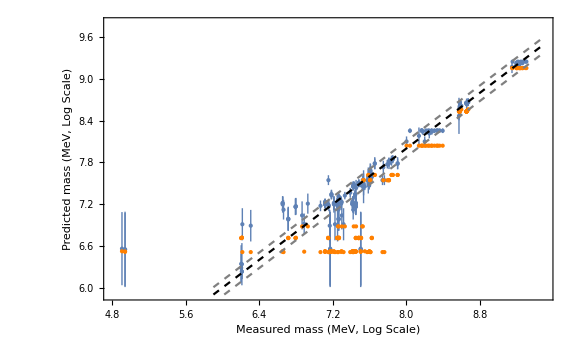

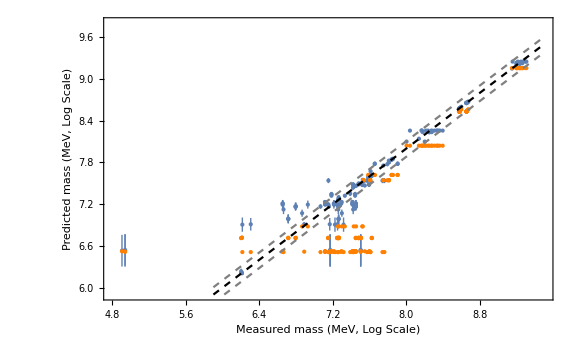

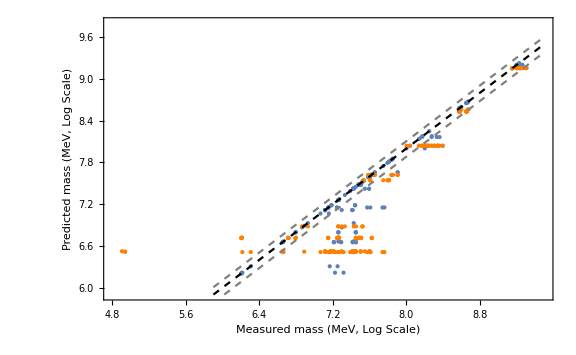

plots/fig2a.pdf

plots/NNMesons80QM.pdf

plots/fig2b.pdf

plots/NNMesons100QM.pdf

plots/fig2c.pdf

plots/GPMesonsQM.pdf

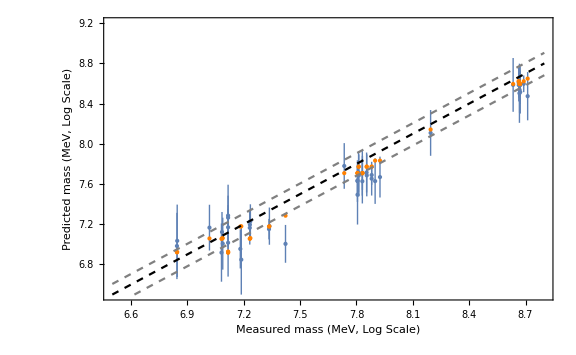

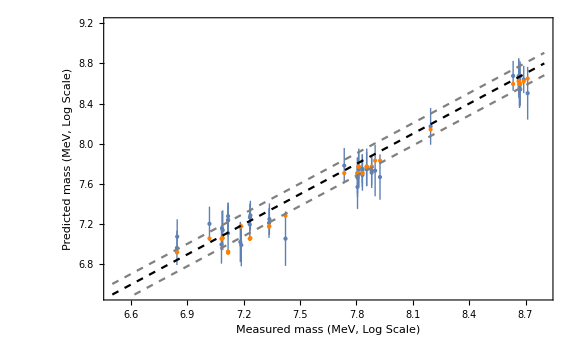

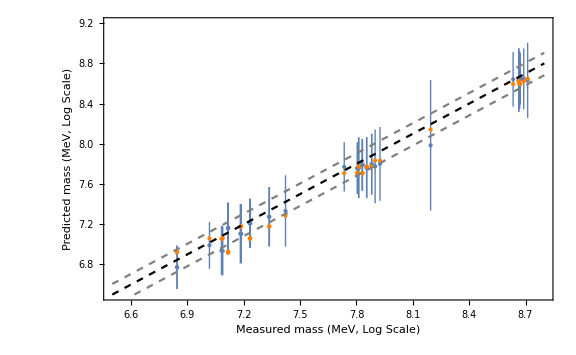

plots/fig3a.pdf

plots/NNBaryons80QM.pdf

plots/fig3b.pdf

plots/NNBaryons100QM.pdf

plots/fig3c.pdf

plots/GPBaryonsQM.pdf

```mathematica
(*predictions for mesons *)
PR1={{4.8,9.5},{5.9,9.8}};
fig2a=funcPlotQM[MesonicData80,QmodelM,PR1]
fig2b=funcPlotQM[MesonicData100,QmodelM,PR1]
fig2c=funcPlotQM[M,QmodelM,PR1]

Export["plots/fig2a.pdf",fig2a]
Export["plots/NNMesons80QM.pdf",fig2a]
Export["plots/fig2b.pdf",fig2b]
Export["plots/NNMesons100QM.pdf",fig2b]
Export["plots/fig2c.pdf",fig2c]
Export["plots/GPMesonsQM.pdf",fig2c]

(*predictions for baryons *)
PR2={{6.5,8.8},{6.5,9.2}};
fig3a=funcPlotQM[BaryonicData80,QmodelB,PR2]
fig3b=funcPlotQM[BaryonicData100,QmodelB,PR2]
fig3c=funcPlotQM[B,QmodelB,PR2]

Export["plots/fig3a.pdf",fig3a]
Export["plots/NNBaryons80QM.pdf",fig3a]
Export["plots/fig3b.pdf",fig3b]
Export["plots/NNBaryons100QM.pdf",fig3b]
Export["plots/fig3c.pdf",fig3c]
Export["plots/GPBaryonsQM.pdf",fig3c]

(*(*predictions for exotics *)
PR3={{6.2,9.5},{6.2,10.2}};
funcPlotQM[Ex,QmodelE,PR3]
Export["plots/GPExoticsQM.pdf",%]
(*predictions for mesons *)
funcPlotQMNoLines[M,QmodelM,PR1]
Export["plots/GPMesonsQMNoLines.pdf",%];
(*predictions for baryons *)
funcPlotQMNoLines[B,QmodelB,PR2]
Export["plots/GPBaryonsQMNoLines.pdf",%];
(*predictions for exotics *)
funcPlotQMNoLines[Ex,QmodelE,PR3]
Export["plots/GPExoticsQMNoLines.pdf",%];*)
```

```mathematica
allinputs=Join[Minputs,Binputs,Einputs,IdentityMatrix[13]];
```

```mathematica
Dimensions[allinputs]
```

{277,13}

```mathematica
Table[Sort[DD[allinputs[[;;,i]]]],{i,13}]//Column
```

{0,1,2,3}
{0,1}
{0,1,2,3,4}
{0,1,2}
{0,1,2,3}
{0,1}
{0,1,2}
{0,1}
{0,1}
{0,1}
{0,1/2,1,3/2}
{0,1/2,1,3/2,2,3,4}
{-1,0,1}

```mathematica
lists=Join[Table[Range[0,4],{i,10}],{Range[0,3/2,1/2]},{Range[0,4,1/2]},{Range[-1,1,1]}];
lists=Table[Sort[DD[allinputs[[;;,i]]]],{i,13}];
onetokencoding[val_,list_]:=UnitVector[Length[list],Position[list,val][[1,1]]]
CategoricalEncoding[inputs_,lists_]:=Return[Table[Flatten[Table[onetokencoding[inputs[[j]][[i]],lists[[i]]],{i,Length[inputs[[1]]]}]],{j,Length[inputs]}]];
```

```mathematica
MinputsC=CategoricalEncoding[Minputs,lists];
BinputsC=CategoricalEncoding[Binputs,lists];
EinputsC=CategoricalEncoding[Einputs,lists];
UinputsC=CategoricalEncoding[IdentityMatrix[13],lists];
```

```mathematica
(*Put[MinputsC,"data/MesonInputs_C.txt"]
Put[BinputsC,"data/BaryonInputs_C.txt"]
Put[EinputsC,"data/ExoticInputs_C.txt"]
Put[UinputsC,"data/UnitInputs_C.txt"]*)
```

```mathematica
(*Export["data/MesonInputs_C.mat",MinputsC]
Export["data/BaryonInputs_C.mat",BinputsC]
Export["data/ExoticInputs_C.mat",EinputsC]
Export["data/UnitInputs_C.mat",UinputsC]*)
```

```mathematica
Table[Sort[DD[#[[;;,i]]]]&/@{Minputs,Binputs,Einputs},{i,13}]//Column
```

{{0,1},{0,1,2,3},{0,1,2,3}}
{{0,1},{0},{0,1}}
{{0,1},{0,1,2,3},{0,1,2,3,4}}
{{0,1},{0},{0,1,2}}
{{0,1},{0,1,2,3},{0,1}}
{{0,1},{0},{0,1}}
{{0,1},{0,1,2},{0,1}}
{{0,1},{0},{0,1}}
{{0,1},{0,1},{0,1}}
{{0,1},{0},{0,1}}
{{0,1/2,1},{0,1/2,1,3/2},{0,1/2,1}}
{{0,1,2,3,4},{1/2,3/2},{0,1/2,1,3/2,2}}
{{-1,1},{1},{-1,1}}

```mathematica
Length[DD[Minputs]]
```

109

```mathematica
Length[Minputs]
```

196

```mathematica
(*adding a 14th feature such that 
if\vec{v} corresponds to a unique entry,the 14th element is zero by default.Else,if\vec{v} corresponds to m entries,index them 0,...,m-1*)
```

```mathematica
Clear[x]
```

```mathematica
(**)
poss=Flatten[Position[Minputs,#]]&/@Minputs;

r=0;
Minputs1=Transpose[Join[Transpose[Minputs],{Table[r,{i,0,Length[Minputs]-1}]}]];

(*list=Join[{0},Table[1/Prime[100+i],{i,100,1,-1}]];
list={0,3,14,159,2653,58979};
list={0,3,14,15,9};
list=Join[{0},Table[i,{i,100}]];*)
(*list=Join[{0},Table[RandomReal[],{i,100}]];*)
(*list=Table[RandomReal[{0,1}],{i,100}];*)

Do[pos=poss[[j]];
list=Table[(*RandomReal[{-10,10}]*)i,{i,0,Length[pos]-1}];
(*list=Table[i-1,{i,Length[pos]}]//RandomSample;*)
(*list=RandomReal[{-1,1},Length[pos]];*)
Do[
Minputs1[[pos[[i]],-1]]=list[[i]],{i,Length[pos]}],{j,Length[poss]}]

(**)Binputs1=Transpose[Join[Transpose[Binputs],{Table[r,{i,0,Length[Binputs]-1}]}]];

(**)
Einputs1=Transpose[Join[Transpose[Einputs],{Table[r,{i,0,Length[Einputs]-1}]}]];

(**)
Uinputs1=Transpose[Join[Transpose[IdentityMatrix[13]],{Table[r,{i,0,Length[IdentityMatrix[13]]-1}]}]];

Export["data/mesoninputs14.dat",Minputs1//N]
Export["data/baryoninputs14.dat",Binputs1//N]
Export["data/exinputs14.dat",Einputs1//N]
Export["data/unitinputs14.dat",Uinputs1//N]
```

data/mesoninputs14.dat

data/baryoninputs14.dat

data/exinputs14.dat

data/unitinputs14.dat

```mathematica
Flatten[Sort[Select[poss,Length[#]==1&]]]//DD
Length[%]
```

{11,42,49,51,56,57,58,65,69,70,75,76,77,79,82,83,86,105,106,107,114,115,116,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,138,139,140,141,144,145,146,147,148,149,156,157,158,159,160,161,162,165,172,180,187}

60

```mathematica
DD[Sort[poss]]//Length
```

109

```mathematica
Abs[100*(#[[1]]-#[[2]])/#[[1]]]&/@(MinMax[Mtrue[[#]]]&/@poss)
```

{51.9101,51.9101,52.9465,14.9773,17.7208,11.9774,11.9774,11.9774,11.3752,6.30003,0.,7.21117,1.29289,4.17737,4.17737,4.17737,4.17737,4.17737,4.17737,8.51544,1.29289,14.9773,52.9465,51.9101,51.9101,3.58044,3.58044,3.58044,17.7208,11.9774,11.9774,11.9774,14.9773,0.099891,0.099891,11.3752,4.17737,11.9774,11.9774,6.30003,17.7208,0.,11.9774,11.9774,11.9774,4.17737,4.17737,4.17737,0.,11.3752,0.,1.69838,2.32364,2.32364,7.21117,0.,0.,0.,11.9774,11.9774,11.9774,3.58044,3.58044,3.58044,0.,52.9465,51.9101,51.9101,0.,0.,1.69838,2.32364,2.32364,8.51544,0.,0.,0.,8.51544,0.,8.51544,8.51544,0.,0.,0.,0.,0.,8.15822,8.15822,8.15822,9.58417,9.65439,9.65439,1.37126,1.37126,1.37126,1.37126,1.37126,1.37126,9.58417,9.65439,9.65439,8.15822,8.15822,8.15822,0.,0.,0.,9.58417,9.65439,9.65439,0.342412,0.342412,0.342412,0.,0.,0.,0.342412,0.342412,0.342412,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.24723,3.24723,0.,0.,0.,0.,3.24723,3.24723,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.47551,4.42843,0.,2.41002,2.41002,1.21376,2.47551,4.42843,4.42843,0.,2.41002,1.21376,4.42843,2.41002,4.42843,2.41002,4.42843,0.,1.64006,0.403858,0.661395,0.661395,0.650882,1.64006,0.,0.403858,0.661395,0.650882,1.64006,0.661395,0.650882,1.64006,1.64006,1.64006}

```mathematica
Abs[100*(#[[1]]-#[[2]])/#[[1]]]&/@(MinMax[Mtrue[[#]]]&/@poss);
{%//Mean,%//Total}
Abs[100*(#[[1]]-#[[2]])/#[[1]]]&/@(MinMax[Exp[Mtrue[[#]]]]&/@poss);
{%//Mean,%//Total}
```

{5.8096,1138.68}

{88.6559,17376.6}

```mathematica
poss[[9]]
Minputs[[poss[[9]]]]//DD
Mtrue[[poss[[9]]]]//Exp
```

{9,36,50}

{{0,0,1,1,0,0,0,0,0,0,0,1,-1}}

{782.65,1420.,1670.}

```mathematica
Tally[Length/@poss]//Sort
```

{{1,60},{2,56},{3,36},{4,12},{5,20},{6,12}}

```mathematica
poss
```

{{1,24,67},{2,25,68},{3,23,66},{4,22,33},{5,29,41},{6,31,38,44,60},{7,32,39,45,61},{8,30,43,59},{9,36,50},{10,40},{11},{12,55},{13,21},{14,17,37,46},{15,18,47},{16,19,48},{14,17,37,46},{15,18,47},{16,19,48},{20,74,78,80,81},{13,21},{4,22,33},{3,23,66},{1,24,67},{2,25,68},{26,62},{27,63},{28,64},{5,29,41},{8,30,43,59},{6,31,38,44,60},{7,32,39,45,61},{4,22,33},{34,35},{34,35},{9,36,50},{14,17,37,46},{6,31,38,44,60},{7,32,39,45,61},{10,40},{5,29,41},{42},{8,30,43,59},{6,31,38,44,60},{7,32,39,45,61},{14,17,37,46},{15,18,47},{16,19,48},{49},{9,36,50},{51},{52,71},{53,72},{54,73},{12,55},{56},{57},{58},{8,30,43,59},{6,31,38,44,60},{7,32,39,45,61},{26,62},{27,63},{28,64},{65},{3,23,66},{1,24,67},{2,25,68},{69},{70},{52,71},{53,72},{54,73},{20,74,78,80,81},{75},{76},{77},{20,74,78,80,81},{79},{20,74,78,80,81},{20,74,78,80,81},{82},{83},{84,85},{84,85},{86},{87,102},{88,103},{89,104},{90,99,108},{91,100,109},{92,101,110},{93,96},{94,97},{95,98},{93,96},{94,97},{95,98},{90,99,108},{91,100,109},{92,101,110},{87,102},{88,103},{89,104},{105},{106},{107},{90,99,108},{91,100,109},{92,101,110},{111,117},{112,118},{113,119},{114},{115},{116},{111,117},{112,118},{113,119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136,142},{137,143},{138},{139},{140},{141},{136,142},{137,143},{144},{145},{146},{147},{148},{149},{150,153},{151,154},{152,155},{150,153},{151,154},{152,155},{156},{157},{158},{159},{160},{161},{162},{163,169},{164,170,171,175,177,179},{165},{166,167,173,176,178},{166,167,173,176,178},{168,174},{163,169},{164,170,171,175,177,179},{164,170,171,175,177,179},{172},{166,167,173,176,178},{168,174},{164,170,171,175,177,179},{166,167,173,176,178},{164,170,171,175,177,179},{166,167,173,176,178},{164,170,171,175,177,179},{180},{181,186,191,194,195,196},{182,188},{183,184,189,192},{183,184,189,192},{185,190,193},{181,186,191,194,195,196},{187},{182,188},{183,184,189,192},{185,190,193},{181,186,191,194,195,196},{183,184,189,192},{185,190,193},{181,186,191,194,195,196},{181,186,191,194,195,196},{181,186,191,194,195,196}}

```mathematica
Binputs//DD//Length
```

41

```mathematica
Einputs//DD//Length
```

20

```mathematica
Einputs//Length
```

25

```mathematica
Minputs1[[;;,-1]]//DD//Length
```

196